```mathematica
(*Columns*)
(*Resistor, Average Voltage, StdEV Voltage, Average Voltage Squared, StdEV Voltage Squared*)

ex4 = Import["./Documents/Lab_6_Data_Analysis/ex4-11.csv"];
```

```mathematica
col1 = ex4[[All, 1]][[2 ;; 9]];
col2 = ex4[[All, 2]][[2 ;; 9]];
col3 = ex4[[All, 3]][[2 ;; 9]];
col4 = ex4[[All, 4]][[2 ;; 9]];
col5 = ex4[[All, 5]][[2 ;; 9]];
```

FittedModel[0.368924+0.334468 x]

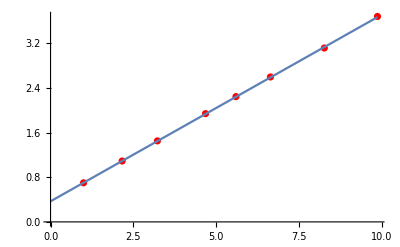
-Graphics-V.b2 (mV).b2R(kΩ)

```mathematica
(*Plot Voltage-Squared vs Resistance*)
ex4plotpair = {col1, col4};
ex4plotTuple = Transpose[ex4plotpair];
ListPlot[ex4plotTuple, PlotMarkers->{"O"}];

(*Weighted Least Square Fit*)
sim=Flatten[MapThread[Function[{a},{#1[[1]],a}]/@RandomVariate[NormalDistribution[#1[[2]],#2],200]&,{ex4plotTuple,col5}],1];
fit2=LinearModelFit[ex4plotTuple,x,x,Weights->1/col5]
Labeled[
Show[
ListPlot[ex4plotTuple,PlotStyle->Red],
Plot[{fit2[x]},{x,0,ex4plotTuple[[-1,1]]}]   ],
{"V.b2 (mV).b2", "R(kΩ)"},
{Left, Bottom},
RotateLabel->True
]
```

```mathematica
(*Residual Graph*)

(*Columns*)
(*Resistor, Average Voltage, StdEV Voltage, Average Voltage Squared, StdEV Voltage Squared, Predicted Voltage Squared, Residuals*)
```

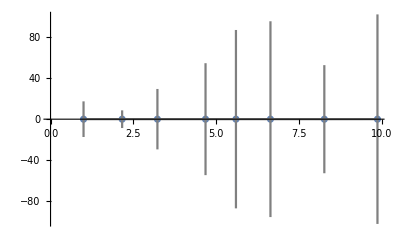
-Graphics-V.b2 (mV).b2R(kΩ)

```mathematica
ex4err = Import["./Documents/Lab_6_Data_Analysis/ex4-11_errs.csv"];
col6 = ex4err[[All, 6]][[2 ;; 9]]; (* Predicted Voltage *)
col7 = ex4err[[All, 7]][[2 ;; 9]];   (* Residuals *)                                    

ex4plotpairerrs = {col1, col7};
ex4plotTuplerrs = Transpose[ex4plotpairerrs]; (*x, y*)

ex4plotpairerrs2 = {col1, col7, col5};
ex4plotTuplerrs2= Transpose[ex4plotpairerrs2]; (*x, y, errs*)

Needs["ErrorBarPlots`"]
Labeled[
	Show[
	ListPlot[ex4plotTuplerrs, PlotRange->{-100, 100}],     (*Note the Range*)
	Plot[lm[x],{x,0,12}],
	ErrorListPlot[ex4plotTuplerrs2,PlotStyle->Gray, Joined-> True]
   ],
{"V.b2 (mV).b2", "R(kΩ)"},
{Left, Bottom},
RotateLabel->True
]
```